```mathematica
ME314 Final Project;
FeiyuChen;
This is the __main__ file of my project;
```

```mathematica
(*Quit[]*)
(*Open and run all other Mathematica scripts*)
(*myOpenFile[filename_]:=Module[{nb1},nb1=NotebookOpen[NotebookDirectory[]<>"/"<>filename];
     SelectionMove[nb1,All,Notebook];
     SelectionEvaluate[nb1]
]
myOpenFile["funcs_math.nb"];
myOpenFile["funcs_assist.nb"];
myOpenFile["funcs_main.nb"];*)
```

```mathematica
(*Put your code here to create links system*)
CreateObjects:=Module[{},

(* ------ Output of createLink ------
The link class returned by createLink has 5 elements;
{T,pFront,pBack,TFront,TBack};

You need to access them by index;
IdxT=1;IdxPFront=2;IdxPBack=3;IdxTFront=4;IdxTBack=5;
Such as:
link1=createLink3DOFpp[p0,p1]
link1[[IdxTFront]]
*)

(* Example 1: Triangle *)
nthGroup=1;
initRandVelocity=0.5;

p0={-0.5,0};
p1={0.5,0.5};
l=CalcDistpp[p0,p1];

link1=createLink3DOFpp[p0,p1];
link2=createLink0DOFgθl[link1[[IdxTFront]],Pi*2/3,l];
link3=createLink0DOFgθl[link2[[IdxTFront]],Pi*2/3,l];

(* Example 2: links *)
(*
nthGroup=2;
initRandVelocity=0;

gFix=Trans4[0.5,0.5];
createVertex[gFix];
link4=createLink1DOFgθl[gFix,0,0.7];
link5=createLink1DOFgθl[link4[[IdxTFront]],0,0.7];
link6=createLink1DOFgθl[link5[[IdxTFront]],-Pi/2,0.7];
*)

(* Example 4: A square wall with 4 edges *);
nthGroup=10;
pWalls={{-2,+2},{+2,+2},{+2,-2},{-2,-2}};
AppendTo[pWalls,pWalls[[1]]];
For[i=1,i≤4,i++,
createLink0DOFpp[pWalls[[i]],pWalls[[i+1]]]
];

(* Example 5: A wall in the middle *)
createLink0DOFpp[{0,-2},{0,-1}];

(*----------------- Constraint --------------*)
(*Set constraints*)
(*addConstraint[link1[[IdxPFront]][[2]]==0];
addConstraint[link1[[IdxPFront]][[1]]==0];*)
(*addConstraint[qs[[1]]==0];
addConstraint[qs[[2]]==0];*)
];
```

```mathematica
(* Set up all things *)
mainResetVars;
CreateObjects;
RemoveDuplicateVertexs;

Print["Start Solving ..."];
mainSolveELeqs;
Print["Finish Solving ..."];

Print["Start setting impact ..."];
SetUpImpacts[];
Print["Finish setting impact ..."];
```

Computing simulation: 2.07189 / 3 ...

Computing simulation is completed.

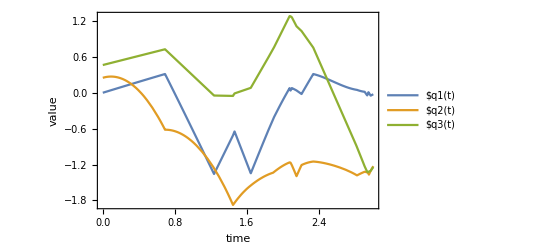

```mathematica
(* Set up params for NDSolve *)
timeend=3;(* total simulation time *)
MAXIMPACTTIMES=100;
impactDetectionError=0.1;
intergrationMaxStepSize=0.01;
ifprint=False;

ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

(* NDsolve and Play simulation *)
{end,data,bounces}=mainNDSolveSimulation[qsInit,dqsInit];

(* Plot *)

plotVariablesValues
plotAnimation
```